## Лабораторная работа №3 Карлович Алексей, Кирилло Дмитрий, Логвиненко Арина 3 курс, 5а группа ММФ БГУ Вариант 4

### Задание 1

```mathematica
xk = {0,π/6,π/4,π/3,π/2};
f = (Cos@#)^2&/@xk
```

{1,3/4,1/2,1/4,0}

```mathematica
w[k_Integer]:=Times@@Drop[xk⟦k⟧-xk,{k}]
```

```mathematica
A[k_]:=1/w[k]
```

```mathematica
A@#&/@Range[Length@xk]
```

{144/π^4,-1296/π^4,2304/π^4,-1296/π^4,144/π^4}

```mathematica
P[x_]:=(∑_(k=1)^(Length@xk) (A[k]f⟦k⟧)/(x-xk⟦k⟧))/(∑_(k=1)^(Length@xk) A[k]/(x-xk⟦k⟧))
```

```mathematica
P[x]
%//Simplify
```

(144/(π^4 x)-324/(π^4 (-π/3+x))+1152/(π^4 (-π/4+x))-972/(π^4 (-π/6+x)))/(144/(π^4 x)+144/(π^4 (-π/2+x))-1296/(π^4 (-π/3+x))+2304/(π^4 (-π/4+x))-1296/(π^4 (-π/6+x)))

((π-2 x) (4 π^2+9 π x-36 x^2))/(4 π^3)

```mathematica
x̃={π/12,(5π)/12,(7π)/24};
P[#]&/@x̃
%//N
```

{15/16,1/16,95/256}

{0.9375,0.0625,0.371094}

### Задание 2

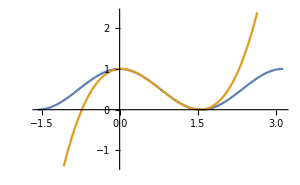

```mathematica
Plot[{(Cos@x)^2,P[x]},{x,-π/2,π}]
```

```mathematica
(Cos@#)^2&/@x̃
%//N
```

{1/8 (1+√3)^2,1/8 (-1+√3)^2,Sin[(5 π)/24]^2}

{0.933013,0.0669873,0.37059}

```mathematica
Abs[((Cos@#)^2-P@#)&/@x̃]//N
```

{0.0044873,0.0044873,0.000503273}